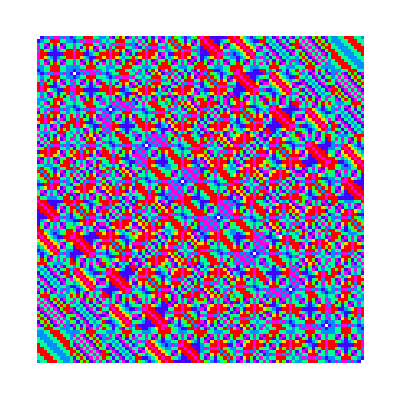

```mathematica
kaprekar[n_,k_]:=FromDigits[PadRight[Reverse[Sort[IntegerDigits[k]]],If[n-Length[IntegerDigits[k]]==0,Length[IntegerDigits[k]],n]]]-FromDigits[PadLeft[Sort[IntegerDigits[k]],If[n-Length[IntegerDigits[k]]==0,Length[IntegerDigits[k]],n]]];count[n_,k_]:=If[Or[kaprekar[n,k]==0,k==6174],0,i=0;Subscript[c, 0]=k;While[Subscript[c, i]≠6174,Subscript[c, i+1]=kaprekar[n,Subscript[c, i]];i=i+1];i];data=Table[count[4,100*x+y],{x,0,99},{y,0,99}];ArrayPlot[data,ColorRules->{0->RGBColor["#FFFFFF"],1->RGBColor["#FEDB01"],2->RGBColor["#4AFD04"],3->RGBColor["#02FE94"],4->RGBColor["#0191FD"],5->RGBColor["#4501FE"],6->RGBColor["#FF00DC"],7->RGBColor["#FE0000"]},FrameTicks->Automatic]
```